# Mathematica for Bioinformatics

by George I. Mias, PhD
["http://georgemias.org"](http://georgemias.org)

## Chapter 11: Time Series

## Time Series

### TimeSeries Function

```mathematica
SeedRandom[123];
intensities=RandomReal[20,20];
times=Range[2,40,2]
```

{2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40}

```mathematica
pairedValues=Transpose[{times,intensities}]
```

{{2,9.11438},{4,19.5565},{6,18.8643},{8,19.2443},{10,6.04696},{12,9.33417},{14,1.23277},{16,7.71289},{18,8.59677},{20,15.5749},{22,0.971811},{24,12.5653},{26,5.55974},{28,1.80435},{30,17.5317},{32,2.18214},{34,5.31515},{36,18.3722},{38,3.39832},{40,1.99157}}

```mathematica
?TimeSeries
```

TimeSeries[{{t_1,v_1},{t_2,v_2}…}] represents a time series specified by time-value pairs {t_i,v_i}.
TimeSeries[{v_1,v_2,…},tspec] represents a time series with values v_i at times specified by tspec.

```mathematica
timeSeriesObject=TimeSeries[intensities,{times}]
```

TimeSeries[…]

```mathematica
timeSeriesObject2=TimeSeries[pairedValues]
```

TimeSeries[…]

```mathematica
Head[timeSeriesObject]
```

TemporalData

```mathematica
Options[TimeSeries]
```

{CalendarType→Gregorian,DateFunction→Automatic,HolidayCalendar→{UnitedStates,Default},MetaInformation→None,MissingDataMethod→None,ResamplingMethod→Automatic,TemporalRegularity→Automatic,ValueDimensions→Automatic,TimeZone:>$TimeZone}

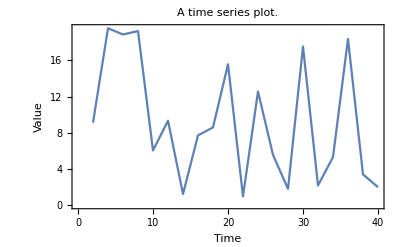

```mathematica
ListLinePlot[timeSeriesObject,
FrameLabel->{"Time","Value"},
Frame->True,
PlotLabel->"A time series plot."]
```

```mathematica
expressionSeries={0.937,1.003,0.966,0.982,1.024,1.073,0.921,1.007,0.913,0.937,1.059,1.479,1.455,1.689,1.312};
```

```mathematica
expressionTemporalData=TimeSeries[expressionSeries,{"September 15 2017",Automatic,"Day"}];
```

```mathematica
expressionTemporalData["Properties"]
```

{DatePath,Dates,FirstDate,FirstTime,FirstValue,LastDate,LastTime,LastValue,Path,PathFunction,PathLength,Times,ValueDimensions,Values}

```mathematica
expressionTemporalData["LastDate"]
```

Fri 29 Sep 2017 00:00:00GMT-5.

```mathematica
expressionTemporalData["Values"]
```

{0.937,1.003,0.966,0.982,1.024,1.073,0.921,1.007,0.913,0.937,1.059,1.479,1.455,1.689,1.312}

```mathematica
expressionTemporalData["September 19 2017"]
```

1.024

```mathematica
{Max[#],Min[#],StandardDeviation[#],Median[#]}&@expressionTemporalData
```

{1.689,0.913,0.244277,1.007}

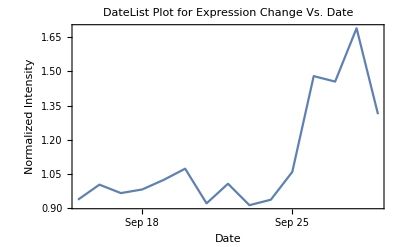

```mathematica
DateListPlot[expressionTemporalData,
PlotLabel-> 
"DateList Plot for Expression Change Vs. Date",
FrameLabel->{"Date","Normalized Intensity"}]
```

```mathematica
?Differences
```

Differences[list] gives the successive differences of elements in list. 
Differences[list,n] gives the n^th differences of list. 
Differences[list,n,s] gives the differences of elements step s apart.
Differences[list,{n_1,n_2,…}] gives the successive n_k^th differences at level k in a nested list.

```mathematica
diffDaily=Differences[expressionTemporalData];
```

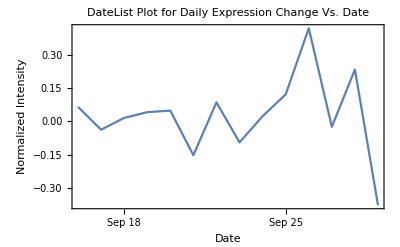

```mathematica
DateListPlot[diffDaily,
PlotLabel-> 
"DateList Plot for Daily Expression Change Vs. Date",
FrameLabel->{"Date","Normalized Intensity"}]
```

### Multiple Time Series Example:

```mathematica
<<MathIOmica`
```

MathIOmica (http://mathiomica.org), by [G. Mias Lab](http://georgemias.org).

```mathematica
rnaExample=Get[FileNameJoin[{ConstantMathIOmicaExamplesDirectory,"rnaExample"}]];
```

```mathematica
rnaExample//Short[#,3]&
```

<|7→<|{FAM138A,RNA}→{{0},{OK}},{OR4F5,RNA}→{{0},{OK}},{LOC729737,RNA}→{{2.73998},{OK}},«25263»,{RNA45S5,RNA}→{{0},{OK}},{DUX4L,RNA}→{{0},{OK}}|>,8→<|«1»|>,«11»,20→<|«1»|>,21→<|«1»|>|>

```mathematica
sampleToDays= <|"7"->"186","8"->"255","9"->"289","10"->"290","11"->"292","12"->"294","13"->"297","14"->"301","15"->"307","16"->"311","17"->"322","18"->"329","19"->"369","20"->"380","21"->"400"|>;
```

```mathematica
sampleList=TimeExtractor[rnaExample]
```

{7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}

```mathematica
exampleRNASampleSeries=CreateTimeSeries[rnaExample];
```

```mathematica
exampleRNASampleSeries[[1;;3]]
```

<|{FAM138A,RNA}→{0,0,0.00257233,0.00206039,0,0,0,0.00429509,0,0,0,0,0,0,0},{OR4F5,RNA}→{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{LOC729737,RNA}→{2.73998,0.555218,5.15563,4.53362,5.71829,0.889102,1.413,2.38838,0.83811,0.706081,2.2049,2.18935,4.05165,2.70102,1.22675}|>

```mathematica
exampleRNASampleSeriesNonConstant=ConstantSeriesClean[exampleRNASampleSeries];
```

Removed series and returning filtered list. If you would like a list of removed keys run the command ConstantSeriesClean[data,ReturnDropped → True].

```mathematica
exampleRNASampleSeriesNonConstant//Short[#,4]&
```

<|{FAM138A,RNA}→{0,0,0.00257233,0.00206039,0,0,0,0.00429509,0,0,0,0,0,0,0},«20711»,{UTY,RNA}→{3.16532,3.28427,3.06644,1.77757,2.90109,2.48543,2.49979,2.65107,0.666915,2.24661,1.49351,1.56608,1.59413,1.13702,0.98188}|>

```mathematica
genesTimeSeriesExample=Query[Keys,1]@exampleRNASampleSeriesNonConstant[[1;;10]]
```

{FAM138A,LOC729737,DDX11L1,WASH7P,MIR6859-1,OR4F16,LOC100132287,LOC100133331,MIR6723,OR4F29}

```mathematica
Length[#]&/@Values@exampleRNASampleSeriesNonConstant[[1;;10]]
```

{15,15,15,15,15,15,15,15,15,15}

```mathematica
dataTimeSeriesExample=Transpose[Values@exampleRNASampleSeriesNonConstant[[1;;10]]];
```

```mathematica
dataTimeSeriesExample//Short[#,5]&
```

{{0,2.73998,6.75461,11.8883,0.256318,0.0053034,1.97164,0.0000580254,20.3672,0.0053034},{0,0.555218,5.22339,6.70585,0,0,0.40352,0.0000695069,43.9099,0},«11»,{0,2.70102,6.59982,7.2482,0,0,0.791959,0.0446897,71.5576,0},{0,1.22675,6.31519,6.8114,0,0,0.462767,0.000176344,50.1361,0}}

```mathematica
exampleRNASampleTemporalData=TimeSeries[dataTimeSeriesExample,{sampleList}];
```

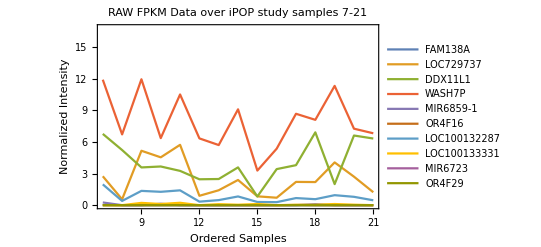

```mathematica
ListLinePlot[exampleRNASampleTemporalData,
PlotLabel-> 
"RAW FPKM Data over iPOP study samples 7-21",
FrameLabel->{"Ordered Samples",
"Normalized Intensity"},
Frame-> True,
PlotLegends->genesTimeSeriesExample]
```

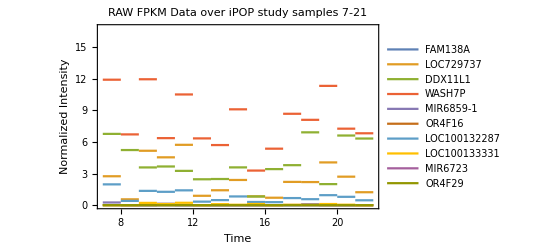

```mathematica
ListStepPlot[exampleRNASampleTemporalData,
PlotLabel-> 
"RAW FPKM Data over iPOP study samples 7-21",
FrameLabel->{"Time","Normalized Intensity"},
Frame-> True,Joined->False,
PlotLegends->
PointLegend[Automatic,genesTimeSeriesExample,
LegendFunction->Panel,LegendMargins->5]]
```

```mathematica
daysList=Values@sampleToDays
```

{186,255,289,290,292,294,297,301,307,311,322,329,369,380,400}

```mathematica
exampleRNADatesTemporalData=TimeSeries[dataTimeSeriesExample,{daysList}];
```

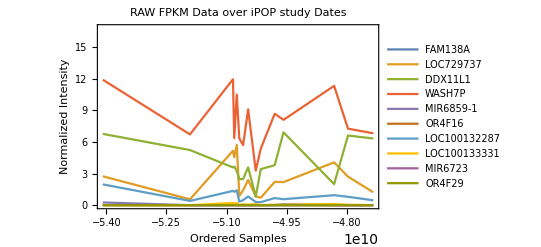

```mathematica
DateListPlot[exampleRNADatesTemporalData,PlotLabel-> "RAW FPKM Data over iPOP study Dates",
FrameLabel->{"Ordered Samples",
"Normalized Intensity"},Frame-> True,
PlotLegends->PointLegend[Automatic,
genesTimeSeriesExample,
LegendFunction->Panel,LegendMargins->5]]
```

## Vignette: FinancialData

```mathematica
FinancialData["ILMN","Name"]
```

Illumina

```mathematica
FinancialData["ILMN","Sector"]
```

Biotechnology

```mathematica
ilm=TimeSeries[FinancialData["ILMN",{2000}]];
```

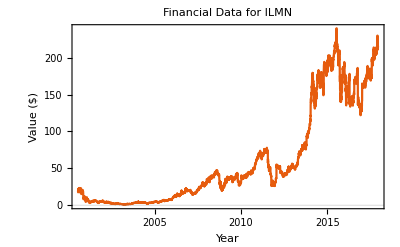

```mathematica
DateListPlot[ilm,
PlotTheme->"Scientific",
PlotLabel-> "Financial Data for ILMN",
FrameLabel-> {"Year","Value ($)"}]
```

```mathematica
manufacturers=FinancialData["DrugManufacturers-Major","Members"];
```

```mathematica
manufacturers//Short
```

{AMEX:AXN,AMEX:CPHI,AX:ANP,AX:AVX,AX:CIR,«69»,PK:SCLR,PK:TRAB,SI:A61,SI:E02}

```mathematica
biotechnology=FinancialData["Biotechnology"];
```

```mathematica
biotechnology//Short
```

{AMEX:BTX,AMEX:CRMD,AMEX:CUR,AMEX:CVM,AMEX:HEB,«230»,V:QPT,V:SBM,V:SSS,V:VPI}

## Time Series ModelFit

```mathematica
{{"Model","Parameter","Family"},{"AR",{p},autoregressive model family},{"MA",{q},moving-average model family},{"ARMA",{p,q},autoregressive moving-average model family},{"ARIMA",{p,d,q},integrated ARMA model family},{"SARMA",{{p,q},{sp,sq},s},seasonal ARMA model family},{"SARIMA",{{p,d,q},{sp,sd,sq},s},seasonal ARIMA model family},{"ARCH",{q},ARCH model family},{"GARCH",{q,p},GARCH model family}}//Dataset
```

Dataset[<>]

```mathematica
roBMI=ResourceObject["BMI by Country"];
```

```mathematica
roBMI["Description"]
```

Estimated mean Body Mass Index (BMI) trend by country

```mathematica
roBMI["Details"]
```

Estimated mean Body Mass Index (BMI) trend between 1975 and 2014 by country. 
BMI (kg/m2) estimates are from male/female populations over the age of 18.

```mathematica
roBMI["InformationElements"]
```

<|Length→382,Dimensions→{382,3}|>

```mathematica
FullForm@roBMI["ReleaseDate"]
```

DateObject[List[2017,6,16],"Day","Gregorian",-4.]

```mathematica
dataBMI=ResourceData["BMI by Country"];
```

```mathematica
Head[dataBMI]
```

Dataset

```mathematica
Normal[Query[1,Keys]@dataBMI]
```

{Country,Gender,BMI}

```mathematica
Normal[Query[1,Values,Head[#]&]@dataBMI]
```

{Entity,String,TemporalData}

### USA BMI Data Modeling

```mathematica
usaBMI=Query[Select[MatchQ[#Country,Entity["Country","UnitedStates"]]&]]@dataBMI;
```

```mathematica
Head[#]&/@#&/@(Normal@usaBMI)
```

{<|Country→Entity,Gender→String,BMI→TemporalData|>,<|Country→Entity,Gender→String,BMI→TemporalData|>}

```mathematica
timeSeriesUSABMImale=Query[1,"BMI"]@usaBMI;
```

```mathematica
timeSeriesUSABMIfemale=Query[2,"BMI"]@usaBMI;
```

```mathematica
Mean[{timeSeriesUSABMImale,timeSeriesUSABMIfemale}]
```

TimeSeries[…]

```mathematica
lengthBMI=timeSeriesUSABMIfemale["PathLength"]
```

40

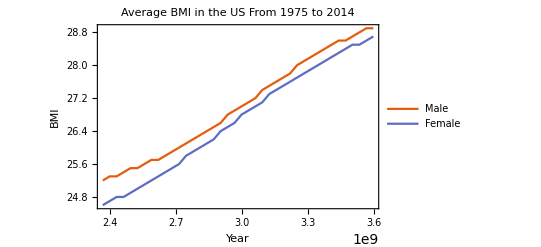

```mathematica
DateListPlot[{timeSeriesUSABMImale,
timeSeriesUSABMIfemale},
PlotTheme->"Scientific",
PlotLabel->
("Average BMI in the US From 1975 to 2014"),
PlotLegends->{"Male","Female"},
FrameLabel->{"Year","BMI"}]
```

```mathematica
modelUSABMIfemale=
TimeSeriesModelFit[timeSeriesUSABMIfemale,"AR"];
```

```mathematica
modelUSABMImale=
TimeSeriesModelFit[timeSeriesUSABMImale,"AR"];
```

```mathematica
modelUSABMIfemale["Properties"]
```

{ACFPlot,ACFValues,AIC,AICc,BIC,BestFit,BestFitParameters,CandidateModels,CandidateModelSelectionValues,CandidateSelectionTable,CandidateSelectionTableEntries,CovarianceMatrix,ErrorVariance,FitResiduals,ForecastStandardErrors,InformationMatrix,LjungBoxPlot,LjungBoxValues,ModelFamily,PACFPlot,PACFValues,ParameterConfidenceIntervals,ParameterTable,ParameterTableEntries,PredictionLimits,Properties,SBC,SelectionCriterion,StandardizedResiduals,TemporalData}

```mathematica
modelUSABMIfemale["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
𝒶_1 | 0.93382 | 0.0565642 | 16.509 | 9.29499×10^-20

```mathematica
modelUSABMIfemale["BestFit"]
```

ARProcess[1.76485,{0.93382},0.215031]

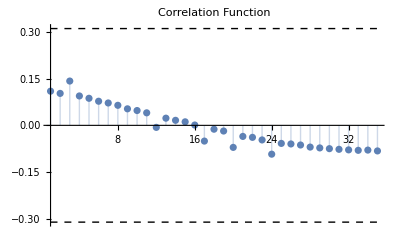
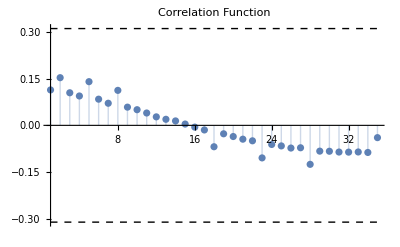
Female | -Graphics-
Male | -Graphics-

```mathematica
TableForm[#,TableHeadings->
{{"Female","Male"},None}]&@
(#["ACFPlot"]&/@
{modelUSABMIfemale,modelUSABMImale})
```

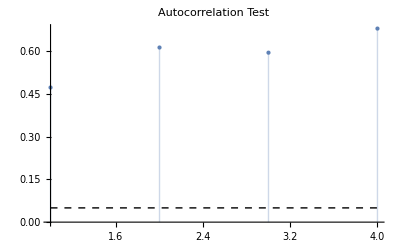

```mathematica
modelUSABMIfemale["LjungBoxPlot"]
```

```mathematica
modelUSABMIfemaleAutomatic=
TimeSeriesModelFit[timeSeriesUSABMIfemale,Automatic];
```

```mathematica
modelUSABMImaleAutomatic=
TimeSeriesModelFit[timeSeriesUSABMImale,Automatic];
```

```mathematica
modelUSABMIfemaleAutomatic["BestFit"]
```

ARIMAProcess[0.105128,{},1,{},0.00151216]

```mathematica
modelUSABMImaleAutomatic["BestFit"]
```

ARIMAProcess[0.0948718,{},1,{},0.00202498]

```mathematica
modelUSABMIfemaleAutomatic["CandidateSelectionTable"]
```

| Candidate | AIC
1 | ARIMAProcess[0,1,0] | -255.769
2 | ARIMAProcess[0,1,1] | -253.782
3 | ARIMAProcess[1,1,0] | -253.781
4 | ARIMAProcess[1,2,1] | -251.5
5 | ARIMAProcess[1,1,1] | -251.354
6 | ARIMAProcess[1,2,2] | -248.683
7 | ARIMAProcess[2,2,1] | -248.319
8 | ARIMAProcess[2,2,2] | -246.412
9 | ARIMAProcess[0,2,1] | -244.195
10 | ARIMAProcess[1,2,0] | -237.821

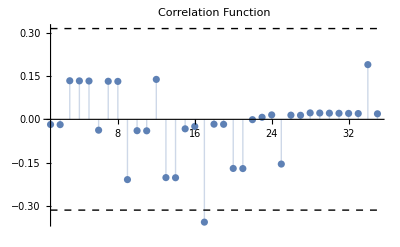
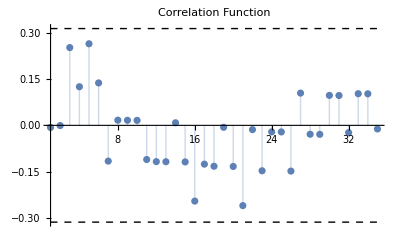
Female | -Graphics-
Male | -Graphics-

```mathematica
TableForm[#,TableHeadings->
{{"Female","Male"},None}]&@
(#["ACFPlot"]&/@{modelUSABMIfemaleAutomatic,
modelUSABMImaleAutomatic})
```

```mathematica
forecastsBMIUS=TimeSeriesForecast[#,{4}]&/@
{modelUSABMIfemaleAutomatic,
modelUSABMImaleAutomatic};
```

```mathematica
forecastsBMIUS[[1]]["Properties"]
```

{Components,DateList,DatePath,DatePaths,Dates,FirstDates,FirstTimes,FirstValues,LastDates,LastTimes,LastValues,MeanSquaredErrors,Part,Path,PathCount,PathFunction,PathFunctions,PathLength,PathLengths,Paths,PathTimes,SliceData,SliceDistribution,TimeList,Times,ValueDimensions,ValueList,Values}

```mathematica
errorsBMIForecastUS=
#["MeanSquaredErrors"]^0.5&/@ forecastsBMIUS;
```

```mathematica
?TimeSeriesThread
```

TimeSeriesThread[f,{tseries_1,tseries_2,…}] combines the tseries_i using the function f.

```mathematica
upperBandFemale=TimeSeriesThread[{1,1}.#&,
{forecastsBMIUS[[1]],errorsBMIForecastUS[[1]]}];
upperBandMale=TimeSeriesThread[{1,1}.#&,
{forecastsBMIUS[[2]],errorsBMIForecastUS[[2]]}];
lowerBandFemale=TimeSeriesThread[{1,-1}.#&,
{forecastsBMIUS[[1]],errorsBMIForecastUS[[1]]}];
lowerBandMale=TimeSeriesThread[{1,-1}.#&,
{forecastsBMIUS[[2]],errorsBMIForecastUS[[2]]}];
```

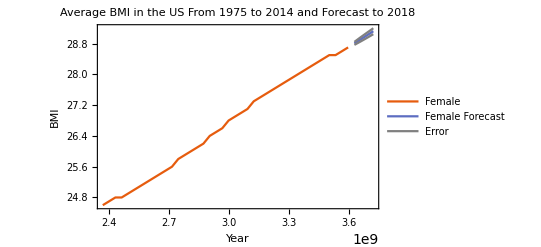

```mathematica
DateListPlot[
{modelUSABMIfemaleAutomatic["TemporalData"],
TimeSeriesForecast[modelUSABMIfemaleAutomatic,
{4}],upperBandFemale,lowerBandFemale},
PlotTheme->"Scientific",
PlotLegends->{"Female","Female Forecast",
"Error",None},
FrameLabel->{"Year","BMI"},
PlotLabel-> "Average BMI in the US From
 1975 to 2014 and Forecast to 2018",
PlotStyle->{Automatic,Automatic,Gray,Gray},
Filling->{3->{4}}]
```

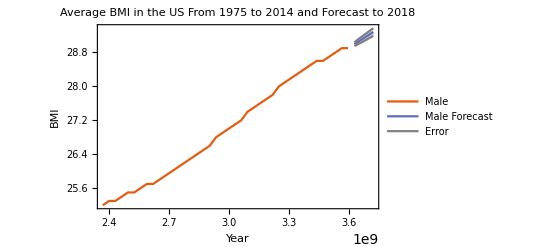

```mathematica
DateListPlot[
{modelUSABMImaleAutomatic["TemporalData"],
TimeSeriesForecast[modelUSABMImaleAutomatic,
{4}],upperBandMale,lowerBandMale},
PlotTheme->"Scientific",
PlotLegends->{"Male","Male Forecast",
"Error",None},
FrameLabel->{"Year","BMI"},
PlotLabel-> "Average BMI in the US 
From 1975 to 2014 and Forecast to 2018",
PlotStyle->{Automatic,Automatic,Gray,Gray},
Filling->{3->{4}}]
```

## Unevenly Sampled Time Series Classification Examples

### Lomb Scargle Classification in MathIOmica

### Classification Simulation Example

```mathematica
SeedRandom[7777];classificationExample1 = Normalize[#]&/@Association[Join[Table["SpikePositive_"<>ToString[i]-> UnitVector[20,1]+RandomReal[{-.1,.1},20],{i,1,10}],
Table["SpikePositive_"<>ToString[i]-> UnitVector[20,3]+RandomReal[{-.1,.1},20],{i,11,20}],
Table["SpikeNegative_"<>ToString[i]-> -UnitVector[20,1]+RandomReal[{-.1,.1},20],{i,1,10}],Table["SpikeNegative_"<>ToString[i]-> -UnitVector[20,3]+RandomReal[{-.1,.1},20],{i,11,20}],Table["LinearPositive_"<>ToString[i]-> Range[20]+RandomReal[{-.1,.1},20],{i,1,10}],Table["LinearPositive_"<>ToString[i]-> 0.2Range[20]+RandomReal[{-.1,.1},20],{i,11,20}],Table["LinearNegative_"<>ToString[i]-> -0.1Range[20]+RandomReal[{-.1,.1},20],{i,1,10}],
Table["LinearNegative_"<>ToString[i]-> -0.2Range[20]+RandomReal[{-.1,.1},20],{i,11,20}],
Table["Sinusoidal1_"<>ToString[i]-> Cos[2Pi*0.65Range[20]]+RandomReal[{-.1,.1},20],{i,1,10}],Table["Sinusoidal2_"<>ToString[i]-> 5Cos[2Pi*0.3Range[20]]+RandomReal[{-.1,.1},20],{i,11,20}],
Table["Sinusoidal3_"<>ToString[i]-> 5Cos[2Pi*0.15*Range[20]]+RandomReal[{-.1,.1},20],{i,21,30}]]];
```

```mathematica
classificationExampleMissing=(Query[All,Nest[ReplacePart[#,RandomInteger[{1,20}]-> Missing[]]&,#,RandomInteger[{1,2}]]&]@classificationExample1);
```

```mathematica
classificationExampleMissing//Short[#,6]&
```

<|SpikePositive_1→{0.966088,-0.0037329,Missing[],0.0610785,0.0398251,«10»,0.0731667,-0.0481196,-0.0272324,0.0690434,0.0282179},«108»,S…0→«1»|>

```mathematica
setTimesExample=Range[20];
```

```mathematica
backgroundExample=SeriesApplier[Normalize,#]&@(Query[All,Nest[ReplacePart[#,RandomInteger[{1,20}]-> Missing[]]&,#,RandomInteger[{1,2}]]&]@ RandomReal[{-.1,.1},{10^5,20}]);
```

```mathematica
bootstrapQ95=QuantileEstimator[backgroundExample,
setTimesExample ]
```

0.886511

```mathematica
bootstrapQ95Spikes=
QuantileEstimator[backgroundExample,
setTimesExample,Method-> "Spikes",
QuantileValue-> .95]
```

<|19→{0.434204,-0.433724},18→{0.445524,-0.445848}|>

```mathematica
classificationLombScargle1=
TimeSeriesClassification[
classificationExampleMissing,
setTimesExample,
LombScargleCutoff-> bootstrapQ95,
SpikeCutoffs->bootstrapQ95Spikes];
```

Method → "LombScargle"

```mathematica
Query[All,
Length[#]-> 
Tally[
StringSplit[Keys[#],"_"][[All,1]]]&]@
classificationLombScargle1
```

<|SpikeMax→20→{{SpikePositive,20}},SpikeMin→18→{{SpikeNegative,18}},f1→40→{{LinearPositive,20},{LinearNegative,20}},f3→10→{{Sinusoidal3,10}},f5→6→{{Sinusoidal2,6}},f6→11→{{SpikeNegative,1},{Sinusoidal1,10}}|>

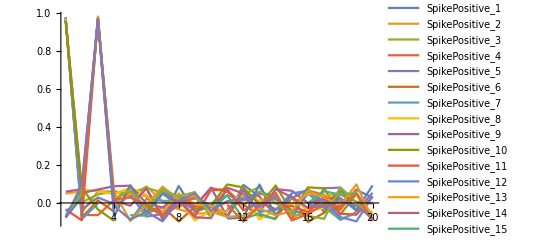
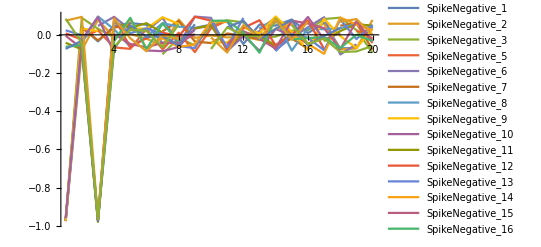
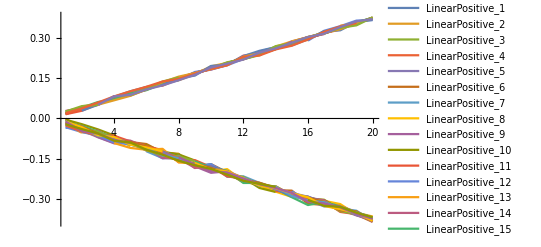
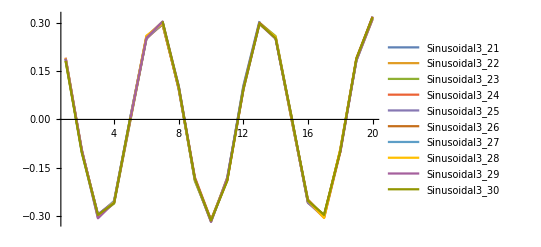
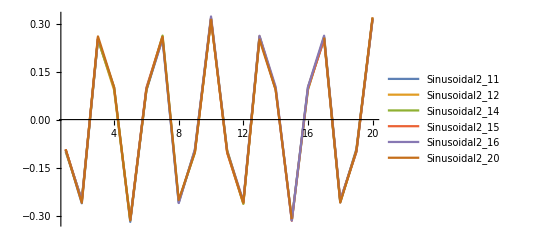
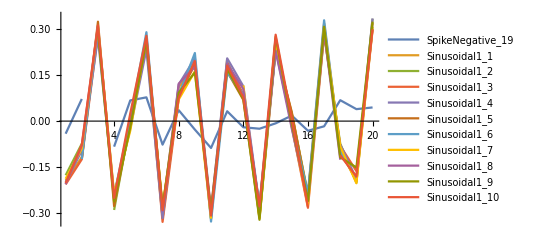
<|SpikeMax→-Graphics-,SpikeMin→-Graphics-,f1→-Graphics-,f3→-Graphics-,f5→-Graphics-,f6→-Graphics-|>

```mathematica
Query[All,
ListLinePlot[#[[All,2]],
PlotRange-> Full,PlotLegends-> PointLegend[Automatic,
LegendFunction->Panel,LegendMargins->15]]&]@
classificationLombScargle1
```

```mathematica
LombScargle[classificationExampleMissing[[1]],
setTimesExample,FrequenciesOnly-> True]
```

<|f1→0.0554017,f2→0.110803,f3→0.166205,f4→0.221607,f5→0.277008,f6→0.33241,f7→0.387812,f8→0.443213,f9→0.498615,f10→0.554017|>

### Classification RNA Sequencing Data Example

#### Time Series Creation

```mathematica
rnaLongitudinal=KeyMap[sampleToDays,rnaExample];
```

```mathematica
rnaLongitudinal[[1;;3,1;;3]]
```

<|186→<|{FAM138A,RNA}→{{0},{OK}},{OR4F5,RNA}→{{0},{OK}},{LOC729737,RNA}→{{2.73998},{OK}}|>,255→<|{FAM138A,RNA}→{{0},{OK}},{OR4F5,RNA}→{{0},{OK}},{LOC729737,RNA}→{{0.555218},{OK}}|>,289→<|{FAM138A,RNA}→{{0.00257233},{OK}},{OR4F5,RNA}→{{0},{OK}},{LOC729737,RNA}→{{5.15563},{OK}}|>|>

```mathematica
rnaQuantileNormed=QuantileNormalization[rnaLongitudinal,ListIndex->1,ComponentIndex->1];
```

```mathematica
rnaZeroTagged=LowValueTag[rnaQuantileNormed,0];
```

```mathematica
rnaZeroTagged[[1;;3,1;;3]]
```

<|186→<|{FAM138A,RNA}→{{Missing[]},{OK}},{OR4F5,RNA}→{{Missing[]},{OK}},{LOC729737,RNA}→{{2.2946},{OK}}|>,255→<|{FAM138A,RNA}→{{0.0000155736},{OK}},{OR4F5,RNA}→{{0.0000155736},{OK}},{LOC729737,RNA}→{{0.494723},{OK}}|>,289→<|{FAM138A,RNA}→{{0.00140424},{OK}},{OR4F5,RNA}→{{0.0000175111},{OK}},{LOC729737,RNA}→{{4.67694},{OK}}|>|>

```mathematica
rnaNoiseAdjusted=LowValueTag[rnaZeroTagged,1,ValueReplacement-> 1.];
```

```mathematica
rnaNoiseAdjusted[[1;;3,1;;3]]
```

<|186→<|{FAM138A,RNA}→{{Missing[]},{OK}},{OR4F5,RNA}→{{Missing[]},{OK}},{LOC729737,RNA}→{{2.2946},{OK}}|>,255→<|{FAM138A,RNA}→{{1.},{OK}},{OR4F5,RNA}→{{1.},{OK}},{LOC729737,RNA}→{{1.},{OK}}|>,289→<|{FAM138A,RNA}→{{1.},{OK}},{OR4F5,RNA}→{{1.},{OK}},{LOC729737,RNA}→{{4.67694},{OK}}|>|>

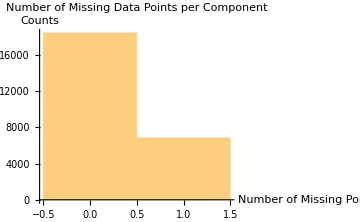

{Missing -> Counts: ,<|0→18427,1→6841|>}

-Graphics-

```mathematica
rnaFiltered=FilterMissing[rnaNoiseAdjusted,3/4,Reference-> "255"];
```

```mathematica
timesRNAiPOP=TimeExtractor[rnaFiltered]
```

{186,255,289,290,292,294,297,301,307,311,322,329,369,380,400}

```mathematica
timeSeriesRNA=CreateTimeSeries[rnaFiltered];
```

```mathematica
timeSeriesRNA[[1;;5]]
```

<|{FAM138A,RNA}→{Missing[],1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{OR4F5,RNA}→{Missing[],1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{LOC729737,RNA}→{2.2946,1.,4.67694,4.48131,4.95507,1.,1.25726,2.14767,1.93219,1.,2.58217,2.31301,4.10284,3.80929,1.45471},{DDX11L1,RNA}→{5.91665,4.32081,3.19599,3.64164,2.7327,2.13461,2.17168,3.23429,1.89576,3.0267,4.34004,7.27001,2.01132,9.27701,7.54415},{WASH7P,RNA}→{10.8594,5.61191,11.1933,6.24138,9.24944,5.35752,4.95971,8.33658,7.26071,4.63689,9.41982,8.54148,11.0612,10.1701,8.13348}|>

```mathematica
?SeriesApplier
```

SeriesApplier[function,data] applies a given function to data, an association of lists, implementing masking for Missing values.

SeriesApplier[function,data] applies a given function to data, an association of lists, implementing masking for Missing values.

```mathematica
timeSeriesRNALog=SeriesApplier[Log,timeSeriesRNA];
```

```mathematica
timeSeriesRNALog[[1;;5]]
```

<|{FAM138A,RNA}→{Missing[],0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{OR4F5,RNA}→{Missing[],0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{LOC729737,RNA}→{0.830556,0.,1.54264,1.49992,1.60041,0.,0.228935,0.764385,0.658653,0.,0.94863,0.838548,1.41168,1.33744,0.374807},{DDX11L1,RNA}→{1.77777,1.46344,1.1619,1.29243,1.00529,0.758282,0.775501,1.17381,0.639619,1.10747,1.46788,1.98376,0.698792,2.22754,2.02077},{WASH7P,RNA}→{2.38503,1.72489,2.41532,1.8312,2.22456,1.6785,1.60135,2.12065,1.98248,1.53404,2.24282,2.14493,2.40345,2.31945,2.09599}|>

```mathematica
rnaCompared=SeriesInternalCompare[timeSeriesRNALog,ComparisonIndex->2];
```

```mathematica
rnaCompared[[1;;5]]
```

<|{FAM138A,RNA}→{Missing[],0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{OR4F5,RNA}→{Missing[],0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{LOC729737,RNA}→{0.830556,0.,1.54264,1.49992,1.60041,0.,0.228935,0.764385,0.658653,0.,0.94863,0.838548,1.41168,1.33744,0.374807},{DDX11L1,RNA}→{0.314326,0.,-0.301545,-0.171011,-0.458154,-0.705162,-0.687943,-0.289634,-0.823824,-0.35597,0.00444068,0.520314,-0.764652,0.764095,0.557328},{WASH7P,RNA}→{0.660143,0.,0.690425,0.10631,0.499672,-0.0463898,-0.123544,0.395761,0.257587,-0.190848,0.517924,0.420043,0.678555,0.594558,0.371097}|>

```mathematica
normedRNACompared=SeriesApplier[Normalize,rnaCompared];
```

```mathematica
normedRNACompared[[1;;5]][[1;;5]]
```

<|{FAM138A,RNA}→{Missing[],0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{OR4F5,RNA}→{Missing[],0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{LOC729737,RNA}→{0.218293,0.,0.40545,0.39422,0.420632,0.,0.0601705,0.200902,0.173112,0.,0.249326,0.220394,0.371029,0.351517,0.0985097},{DDX11L1,RNA}→{0.156411,0.,-0.150051,-0.0850959,-0.22798,-0.350893,-0.342324,-0.144124,-0.40994,-0.177133,0.00220971,0.258911,-0.380495,0.380218,0.27733},{WASH7P,RNA}→{0.391269,0.,0.409217,0.0630104,0.296157,-0.0274954,-0.0732251,0.234569,0.152672,-0.113116,0.306975,0.248961,0.402181,0.352396,0.21995}|>

```mathematica
rnaFinalTimeSeries=ConstantSeriesClean[normedRNACompared];
```

Removed series and returning filtered list. If you would like a list of removed keys run the command ConstantSeriesClean[data,ReturnDropped → True].

```mathematica
rnaFinalTimeSeries[[1;;3]]
```

<|{LOC729737,RNA}→{0.218293,0.,0.40545,0.39422,0.420632,0.,0.0601705,0.200902,0.173112,0.,0.249326,0.220394,0.371029,0.351517,0.0985097},{DDX11L1,RNA}→{0.156411,0.,-0.150051,-0.0850959,-0.22798,-0.350893,-0.342324,-0.144124,-0.40994,-0.177133,0.00220971,0.258911,-0.380495,0.380218,0.27733},{WASH7P,RNA}→{0.391269,0.,0.409217,0.0630104,0.296157,-0.0274954,-0.0732251,0.234569,0.152672,-0.113116,0.306975,0.248961,0.402181,0.352396,0.21995}|>

#### Random Distribution Generation

```mathematica
(*Bootstrap generation of 100,000 series using resampling*)
SeedRandom[12345]
rnaBootstrap=BootstrapGeneral[rnaLongitudinal,100000];
(*1. Quantile Normalization*)rnaBootstrapQuantileNormed=QuantileNormalization[rnaBootstrap,ListIndex-> 1,ComponentIndex-> 1];
(*2. Zero values tagged as Missing*)rnaBootstrapZeroTagged=LowValueTag[rnaBootstrapQuantileNormed,0];
(*3. Values less than 1 replaced*) rnaBootstrapNoiseAdjusted=LowValueTag[rnaBootstrapZeroTagged,1,ValueReplacement-> 1];
(*4 Missing data filtered out*) rnaBootstrapFiltered=FilterMissing[rnaBootstrapNoiseAdjusted,3/4,Reference-> "255",ShowPlots-> False];
(*5. Create time series*) timeSeriesBootstrapRNA=CreateTimeSeries[rnaBootstrapFiltered];
(*6. Apply Log to values*) timeSeriesBootstrapRNALog=SeriesApplier[Log,timeSeriesBootstrapRNA];
(*7. Compare against reference in position 2*)rnaBootstrapCompared=SeriesInternalCompare[timeSeriesBootstrapRNALog,ComparisonIndex->2];
(*8. Normalize to unity*)normedBootstrapRNACompared=SeriesApplier[Normalize,rnaBootstrapCompared];
(*9. Check for and remove constant series*)rnaBootstrapFinalTimeSeries=ConstantSeriesClean[normedBootstrapRNACompared];
```

Removed series and returning filtered list. If you would like a list of removed keys run the command ConstantSeriesClean[data,ReturnDropped → True].

#### Classification and Clustering

```mathematica
q95RNA=QuantileEstimator[rnaBootstrapFinalTimeSeries,timesRNAiPOP]
```

0.860294

```mathematica
q95RNASpikes=QuantileEstimator[rnaBootstrapFinalTimeSeries,timesRNAiPOP,Method-> "Spikes"]
```

<|15→{0.856796,-0.337722},14→{0.884214,-0.348537}|>

```mathematica
rnaClassification=TimeSeriesClassification[rnaFinalTimeSeries,timesRNAiPOP,LombScargleCutoff-> q95RNA,SpikeCutoffs->q95RNASpikes];
```

Method → "LombScargle"

```mathematica
LombScargle[rnaFinalTimeSeries[[1]],timesRNAiPOP,FrequenciesOnly-> True]
```

<|f1→0.00500668,f2→0.0104306,f3→0.0158545,f4→0.0212784,f5→0.0267023,f6→0.0321262,f7→0.0375501|>

```mathematica
Query[All,Length]@rnaClassification
```

<|SpikeMax→829,SpikeMin→5962,f1→116,f2→3,f3→30,f4→128,f5→35,f6→13,f7→61|>

```mathematica
rnaClassification[[1;;2,1;;2]]
```

<|SpikeMax→<|{ATAD3C,RNA}→{{0.0855374,0.204135,0.219303,0.378496,0.5849,0.346012,0.545735},{0.,0.,0.,0.,0.,0.,0.,0.,0.997114,0.,0.,0.,0.,0.075919,0.}},{MMP23B,RNA}→{{0.237345,0.471368,0.335256,0.450949,0.568953,0.201913,0.203105},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.}}|>,SpikeMin→<|{DDX11L1,RNA}→{{0.447167,0.069665,0.842392,0.173482,0.0417282,0.112542,0.202636},{0.156411,0.,-0.150051,-0.0850959,-0.22798,-0.350893,-0.342324,-0.144124,-0.40994,-0.177133,0.00220971,0.258911,-0.380495,0.380218,0.27733}},{LINC01128,RNA}→{{0.0905487,0.406082,0.0297171,0.578597,0.239233,0.658612,0.0154399},{-0.0991061,0.,0.0187721,-0.270964,-0.206247,-0.0847502,-0.145098,-0.0170673,-0.671463,-0.103483,-0.12124,-0.0569299,-0.170415,-0.173748,-0.553712}}|>|>

```mathematica
rnaClusters=TimeSeriesClusters[rnaClassification];
```

```mathematica
Keys@rnaClusters
```

{SpikeMax,SpikeMin,f1,f2,f3,f4,f5,f6,f7}

```mathematica
Query[1,Keys]@rnaClusters
```

{Cluster,InitialSplitCluster,IntermediateClusters,SubsplitClusters,Data,GroupAssociations}

```mathematica
Query["f1","GroupAssociations",Length]@rnaClusters
```

4

```mathematica
Query["f1","GroupAssociations",All,Length]@rnaClusters
```

<|G1S1→80,G1S2→27,G2S1→6,G2S2→3|>

```mathematica
Query["f1","GroupAssociations","G1S2"]@rnaClusters
```

{{POC5,RNA},{EWSR1,RNA},{RCCD1,RNA},{MBLAC1,RNA},{FAM173A,RNA},{CCDC12,RNA},{SDHAF1,RNA},{CTU1,RNA},{CCDC28B,RNA},{EMG1,RNA},{CDK2AP2,RNA},{COA5,RNA},{LOC102288414,RNA},{DRAP1,RNA},{THAP7,RNA},{TRMT112,RNA},{TRIM56,RNA},{ZRSR2,RNA},{STAG3L3,RNA},{STAG3L1,RNA},{ZNF529,RNA},{TNFRSF13B,RNA},{GEMIN6,RNA},{C1orf52,RNA},{MTERF,RNA},{RNF122,RNA},{LINC00921,RNA}}

```mathematica
Query[All,"GroupAssociations",All,Length]@rnaClusters
```

<|SpikeMax→<|G1S1→360,G1S2→46,G1S3→38,G1S4→8,G1S5→10,G1S6→30,G1S7→5,G1S8→194,G1S9→21,G1S10→23,G1S11→21,G1S12→7,G1S13→3,G1S14→63|>,SpikeMin→<|G1S1→5667,G1S2→295|>,f1→<|G1S1→80,G1S2→27,G2S1→6,G2S2→3|>,f2→<|G1S1→2,G2S1→1|>,f3→<|G1S1→2,G1S2→4,G2S1→1,G2S2→4,G3S1→15,G3S2→1,G4S1→2,G4S2→1|>,f4→<|G1S1→79,G1S2→48,G2S1→1|>,f5→<|G1S1→1,G1S2→2,G1S3→4,G2S1→16,G2S2→5,G2S3→7|>,f6→<|G1S1→2,G1S2→4,G2S1→5,G2S2→2|>,f7→<|G1S1→31,G1S2→24,G2S1→4,G2S2→2|>|>

```mathematica
Query["f1","Cluster"]@rnaClusters//Short[#,5]&
```

Cluster[«1»]

#### Heatmaps and Dendrograms

```mathematica
rnaClustersDendrogramsReturn=TimeSeriesClusters[rnaClassification,ReturnDendrograms-> True];
```

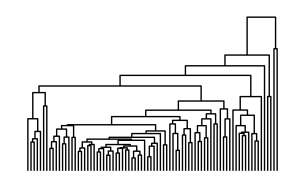
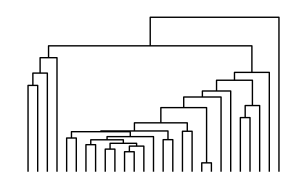
<|{G1S1}→-Graphics-,{G1S2}→-Graphics-|>

```mathematica
Query["f1","G1"]@rnaClustersDendrogramsReturn
```

```mathematica
Query[All,Keys]@rnaClustersDendrogramsReturn
```

<|SpikeMax→{G1},SpikeMin→{G1},f1→{G1,G2},f2→{G1,G2},f3→{G1,G2,G3,G4},f4→{G1,G2},f5→{G1,G2},f6→{G1,G2},f7→{G1,G2}|>

```mathematica
?TimeSeriesDendrogramsHeatmaps
```

TimeSeriesDendrogramsHeatmaps[data] generates a dendrogram and heatmap plots for all classified classes of time series data clusters.

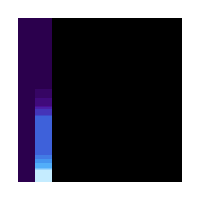
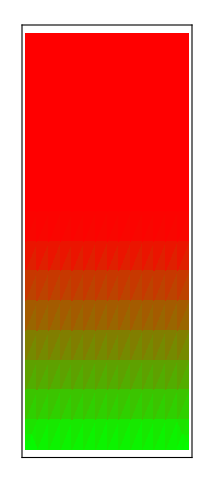
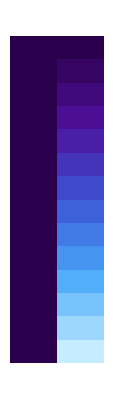
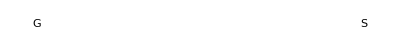
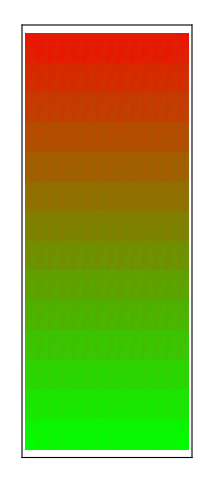
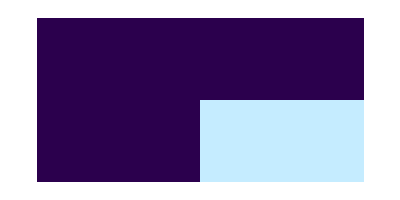
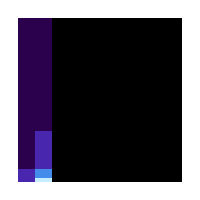
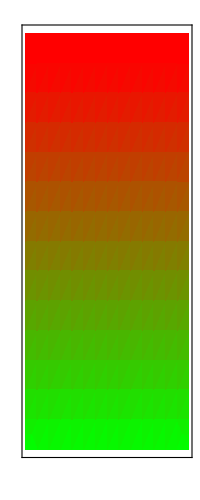
SpikeMax
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Timepoints |  |  | 


SpikeMin
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Timepoints |  |  | 


f1
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Timepoints |  |  | 


f2
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Timepoints |  |  | 


f3
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Timepoints |  |  | 


f4
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Timepoints |  |  | 


f5
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Timepoints |  |  | 


f6
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Timepoints |  |  | 


f7
Dendrogram | HeatMap |  |  | GroupAssociations Index
Group#Subgroup#→Size
-Graphics- | -Graphics- |  | -Graphics- | -Graphics-
 | -Graphics- |  |  | 
 | Timepoints |  |  |

```mathematica
TimeSeriesDendrogramsHeatmaps[rnaClusters,FunctionOptions-> {HorizontalAxisName->"Timepoints"}]
```

#### Annotation and Over Representation Analysis

```mathematica
?GOAnalysis
```

GOAnalysis[data] calculates input data over-representation analysis for Gene Ontology (GO) categories.

```mathematica
goAnalysisRNA=GOAnalysis[rnaClusters,OntologyLengthFilter-> 3,ReportFilter-> 3 ];
```

```mathematica
Query[All,All,Length]@goAnalysisRNA
```

<|SpikeMax→<|G1S1→40,G1S2→10,G1S3→1,G1S4→5,G1S5→1,G1S6→3,G1S7→1,G1S8→189,G1S9→2,G1S10→1,G1S11→1,G1S12→1,G1S13→0,G1S14→17|>,SpikeMin→<|G1S1→2931,G1S2→110|>,f1→<|G1S1→41,G1S2→4,G2S1→0,G2S2→0|>,f2→<|G1S1→0,G2S1→0|>,f3→<|G1S1→0,G1S2→0,G2S1→0,G2S2→0,G3S1→3,G3S2→0,G4S1→0,G4S2→0|>,f4→<|G1S1→6,G1S2→24,G2S1→0|>,f5→<|G1S1→0,G1S2→0,G1S3→1,G2S1→2,G2S2→0,G2S3→0|>,f6→<|G1S1→0,G1S2→1,G2S1→0,G2S2→0|>,f7→<|G1S1→10,G1S2→8,G2S1→0,G2S2→0|>|>

```mathematica
Query["f1","G1S1",1;;2]@goAnalysisRNA
```

<|GO:0005515→{{3.34254×10^-17,2.7576×10^-14,True},{77,8801,47241,48},{{protein binding,molecular_function},{{{PADI4,RNA}},{{USP25,RNA}},{{ZNF207,RNA}},{{ADAM9,RNA}},{{HACE1,RNA}},{{AGO2,RNA}},{{JAK1,RNA}},{{MBP,RNA}},{{KLF3,RNA}},{{FLI1,RNA}},{{PRKDC,RNA}},{{IPO5,RNA}},{{FOCAD,RNA}},{{ELK3,RNA}},{{EFCAB4B,RNA}},{{ARHGEF6,RNA}},{{GTF3C4,RNA}},{{MAPK1,RNA}},{{ANTXR2,RNA}},{{GSK3B,RNA}},{{AHCYL2,RNA}},{{ERAP1,RNA}},{{SAMHD1,RNA}},{{DDX3X,RNA}},{{SSH1,RNA}},{{DNAJC13,RNA}},{{NDUFS1,RNA}},{{AGO1,RNA}},{{FAM168A,RNA}},{{CLPX,RNA}},{{ACLY,RNA}},{{SYNJ2,RNA}},{{INPP4B,RNA}},{{PRKCA,RNA}},{{PTPLB,RNA}},{{PRKAR2A,RNA}},{{CASK,RNA}},{{RUNX1,RNA}},{{PTGER4,RNA}},{{EHD4,RNA}},{{PSME3,RNA}},{{WBP1L,RNA}},{{ADNP2,RNA}},{{AAGAB,RNA}},{{PDK3,RNA}},{{GTF3C3,RNA}},{{HSPA14,RNA}},{{TBC1D22B,RNA}}}}},GO:0005829→{{1.06226×10^-7,0.0000438182,True},{77,3476,47241,21},{{cytosol,cellular_component},{{{PADI4,RNA}},{{AGO2,RNA}},{{JAK1,RNA}},{{CEP78,RNA}},{{PRKDC,RNA}},{{ARHGEF6,RNA}},{{MAPK1,RNA}},{{GSK3B,RNA}},{{AHCYL2,RNA}},{{ERAP1,RNA}},{{AGO1,RNA}},{{ACLY,RNA}},{{SYNJ2,RNA}},{{INPP4B,RNA}},{{PRKCA,RNA}},{{PRKAR2A,RNA}},{{CASK,RNA}},{{PSME3,RNA}},{{IARS2,RNA}},{{AAGAB,RNA}},{{HSPA14,RNA}}}}}|>

```mathematica
EnrichmentReportExport[goAnalysisRNA,OutputDirectory -> $UserDocumentsDirectory,AppendString-> "GOAnalysisRNA"];
```

```mathematica
$UserDocumentsDirectory
```

/Users/george/Documents

```mathematica
keggAnalysisRNA=KEGGAnalysis[rnaClusters,ReportFilter-> 2];
```

```mathematica
Query[All,All,Length]@keggAnalysisRNA
```

<|SpikeMax→<|G1S1→0,G1S2→0,G1S3→1,G1S4→0,G1S5→0,G1S6→0,G1S7→0,G1S8→5,G1S9→0,G1S10→0,G1S11→0,G1S12→0,G1S13→0,G1S14→0|>,SpikeMin→<|G1S1→145,G1S2→8|>,f1→<|G1S1→1,G1S2→0,G2S1→0,G2S2→0|>,f2→<|G1S1→0,G2S1→0|>,f3→<|G1S1→0,G1S2→0,G2S1→0,G2S2→0,G3S1→0,G3S2→0,G4S1→0,G4S2→0|>,f4→<|G1S1→0,G1S2→0,G2S1→0|>,f5→<|G1S1→0,G1S2→0,G1S3→0,G2S1→0,G2S2→0,G2S3→0|>,f6→<|G1S1→0,G1S2→0,G2S1→0,G2S2→0|>,f7→<|G1S1→5,G1S2→1,G2S1→0,G2S2→0|>|>

```mathematica
Query["SpikeMin","G1S1",1;;10,3,1]@keggAnalysisRNA
```

<|path:hsa04142→Lysosome - Homo sapiens (human),path:hsa04120→Ubiquitin mediated proteolysis - Homo sapiens (human),path:hsa04660→T cell receptor signaling pathway - Homo sapiens (human),path:hsa04662→B cell receptor signaling pathway - Homo sapiens (human),path:hsa04210→Apoptosis - Homo sapiens (human),path:hsa01100→Metabolic pathways - Homo sapiens (human),path:hsa05169→Epstein-Barr virus infection - Homo sapiens (human),path:hsa05161→Hepatitis B - Homo sapiens (human),path:hsa01200→Carbon metabolism - Homo sapiens (human),path:hsa04722→Neurotrophin signaling pathway - Homo sapiens (human)|>

```mathematica
Query["SpikeMin","G1S1",1;;10,3,2/*Length]@keggAnalysisRNA
```

<|path:hsa04142→81,path:hsa04120→82,path:hsa04660→68,path:hsa04662→51,path:hsa04210→79,path:hsa01100→423,path:hsa05169→100,path:hsa05161→78,path:hsa01200→65,path:hsa04722→66|>

```mathematica
Query["SpikeMin","G1S1",{3}]@keggAnalysisRNA//Short[#,6]&
```

<|path:hsa04660→{{1.8551×10^-17,1.83655×10^-15,True},{1810,«3»},{T cell receptor signaling pathway - Homo sapiens (human),{{{GRAP2,RNA}},{{NCK2,RNA}},«64»,{{NFKBIA,RNA}},{{JUN,RNA}}}}}|>

```mathematica
pathwaymembers=Query["SpikeMin","G1S1",3,3,2,All,1,1]@keggAnalysisRNA;
```

```mathematica
pathwaymembers//Short
```

{GRAP2,NCK2,ITK,«62»,CD8A,NFKBIA,JUN}

```mathematica
pathKey=First@Keys@Query["SpikeMin","G1S1",{3}]@keggAnalysisRNA
```

path:hsa04660

```mathematica
KEGGPathwayVisual[pathKey]
```

<|Pathway→path:hsa04660,Results→{http://www.kegg.jp/kegg-bin/show_pathway?map=hsa04660}|>

```mathematica
keggVisual=KEGGPathwayVisual[pathKey,MemberSet->pathwaymembers];
```

```mathematica
keggVisual//Short[#,10]&
```

<|Pathway→path:hsa04660,Results→{http://www.kegg.jp/kegg-bin/show_pathway?map=hsa04660&multi_query=hsa%3A9402+%2380b2ff%2C%23000000%0D%0Ahsa%3A8440+%2380b2ff%2C%23000000%0D%0Ahsa%3A3702+%2380b2ff%2C%…C%23000000%0D%0Ahsa%3A387+%2380b2ff%2C%23000000%0D%0Ahsa%3A925+%2380b2ff%2C%23000000%0D%0Ahsa%3A4792+%2380b2ff%2C%23000000%0D%0Ahsa%3A3725+%2380b2ff%2C%23000000%0D%0A}|>

```mathematica
SystemOpen@@Query["Results"]@keggVisual
```

```mathematica
KEGGPathwayVisual["path:hsa04668",ResultsFormat-> "Figure",MemberSet->pathwaymembers]
```